Piecewise[{{1, b≤x}, {x/b, b>x&&x≥0}, {0, True}}]

1/2 (1+Erf[x/(√2 σ)])

1/2 a (1+Erf[x/(√2 σ)])-(-1+a) (Piecewise[{{1, b≤x}, {x/b, b>x&&x≥0}, {0, True}}])

Piecewise[{{0, x<0||b≤x}, {1/b, True}}]

(ⅇ^(-x^2/(2 σ^2)))/(√(2 π) σ)

(a ⅇ^(-x^2/(2 σ^2)))/(√(2 π) σ)-(-1+a) (Piecewise[{{0, x<0||b≤x}, {1/b, True}}])

1

1

1

n Binomial[-1+n,-1+k] ((a ⅇ^(-x^2/(2 σ^2)))/(√(2 π) σ)-(-1+a) (Piecewise[{{0, x<0||b≤x}, {1/b, True}}])) (1/2 a (1+Erf[x/(√2 σ)])-(-1+a) (Piecewise[{{1, b≤x}, {x/b, b>x&&x≥0}, {0, True}}]))^(-1+k) (1-1/2 a (1+Erf[x/(√2 σ)])+(-1+a) (Piecewise[{{1, b≤x}, {x/b, b>x&&x≥0}, {0, True}}]))^(-k+n)

(2^(1/2-k) a ⅇ^(-x^2/(2 σ^2)) n Binomial[-1+n,-1+k] (a (1+Erf[x/(√2 σ)]))^(-1+k) (1-1/2 a (1+Erf[x/(√2 σ)]))^(-k+n))/(√π σ)

n ((1-a)/b+(a ⅇ^(-x^2/(2 σ^2)))/(√(2 π) σ)) Binomial[-1+n,-1+k] (1+((-1+a) x)/b-1/2 a (1+Erf[x/(√2 σ)]))^(-k+n) ((x-a x)/b+1/2 a (1+Erf[x/(√2 σ)]))^(-1+k)

2 (2-a)^-k (1-a/2)^n a^(-1+k) n ((1-a)/b+a/(√(2 π) σ)) Binomial[-1+n,-1+k]

2^(1-n) (2-a)^(-k+n) a^(-1+k) Binomial[-1+n,-1+k]

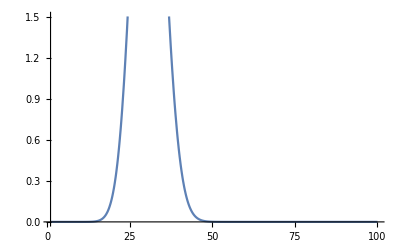

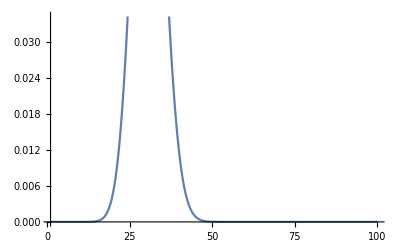

{0.087302,{k→30.4992}}

30

29

```mathematica
Clear[a,b,σ,x,n,k]
(*Define cdf and pdf of uniform[0,b0, N(0,sigma^2) and mixture a*N()+(1-a)*U[]*)
defAssum :=Element[a,Reals]&&a≥0&&a≤1&&Element[b,Reals]&&b>0&&Element[σ,Reals]&&σ>0&&Element[x,Reals]
uniCDF[x_]=Assuming[defAssum,FullSimplify[((Ramp[x]*(UnitStep[x]-UnitStep[x-b]))+b*UnitStep[x-b])/b]]
norCDF[x_]=Assuming[defAssum,FullSimplify[CDF[NormalDistribution[0,σ],x]]]
mixCDF[x_]=Assuming[defAssum,FullSimplify[(1-a)*uniCDF[x]+a*norCDF[x]]]
uniPDF[x_]=Assuming[defAssum,FullSimplify[D[uniCDF[x],x]]]
norPDF[x_]=Assuming[defAssum,FullSimplify[PDF[NormalDistribution[0,σ],x]]]
mixPDF[x_]=Assuming[defAssum,FullSimplify[D[mixCDF[x],x]]]

(*Check if PDFs integrate to one*)
Assuming[defAssum,FullSimplify[Integrate[uniPDF[x],{x,0,b}]]]
Assuming[defAssum,FullSimplify[Integrate[norPDF[x],{x,-Infinity,Infinity}]]]
Assuming[defAssum,FullSimplify[Integrate[mixPDF[x],{x,-Infinity,Infinity}]]]

(*Define order statistic PDF*)
(*For the whole range of x*)
defAssum2 :=Element[a,Reals]&&a≥0&&a≤1&&Element[b,Reals]&&b>0&&Element[σ,Reals]&&σ>0&&Element[x,Reals]&&Element[n,Integers]&&n≥1&&Element[k,Integers]&&1≤k≤n
orderPDF[x_,k_]=Assuming[defAssum2,FullSimplify[n*mixPDF[x]*Binomial[n-1,k-1]*mixCDF[x]^(k-1)*((1-mixCDF[x])^(n-k))]]
(*For x<0 or X>b*)
defAssum3 :=Element[a,Reals]&&a≥0&&a≤1&&Element[b,Reals]&&b>0&&Element[σ,Reals]&&σ>0&&Element[x,Reals]&&x<0&&Element[n,Integers]&&n≥1&&Element[k,Integers]&&1≤k≤n
orderPDF1[x_,k_]=Assuming[defAssum3,FullSimplify[n*mixPDF[x]*Binomial[n-1,k-1]*mixCDF[x]^(k-1)*((1-mixCDF[x])^(n-k))]]
(*For 0≤x≤b*)
defAssum4 :=Element[a,Reals]&&a≥0&&a≤1&&Element[b,Reals]&&b>0&&Element[σ,Reals]&&σ>0&&Element[x,Reals]&&0<x<b&&Element[n,Integers]&&n≥1&&Element[k,Integers]&&1≤k≤n
orderPDF2[x_,k_]=Assuming[defAssum4,FullSimplify[n*mixPDF[x]*Binomial[n-1,k-1]*mixCDF[x]^(k-1)*((1-mixCDF[x])^(n-k))]]
(*maximum of density is located at x=0*)
defAssum5 := Element[a,Reals]&&a≥0&&a≤1&&Element[n,Integers]&&n≥1&&Element[k,Integers]&&1≤k≤n
lik[k_]=Assuming[defAssum5,FullSimplify[orderPDF2[0,k]]]
(*re-wrtining we will see that likelihood is actually a binomial distribution*)
liksimplified[k_] = Assuming[defAssum5,FullSimplify[Binomial[n-1,k-1]*(a/2)^(k-1)*(1-a/2)^(n-k)]]
(*As an example, assume the following parameters.*)
n:=100
a:=0.6
σ:=1
b:=2
(*plot the original likelihood*)
Plot[lik[k],{k,1,n}]
(*plot the simplified likelihood*)
Plot[liksimplified[k],{k,1,n}]
(*Simulation result base on maximizing the resulting function*)
Maximize[{liksimplified[k],1≤k≤n,a≥0,a≤1},{k}]
(*Binomial mode is either at floor[n*a/2] or ceil[n*a/2]-1 we double check the analytical result with maximize function*)
Floor[n*a/2]
Ceiling[n*a/2]-1
```